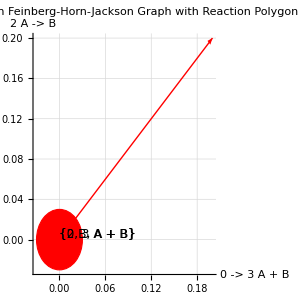

<|Species→{0→3A+B,2A→B},Reactions→strToSymb[{0→3A+B,2A→B,2B→A+B}],Endotactic→True,StronglyEndotactic→True,StoichiometricSubspace→{}|>

```mathematica
ClearAll["Global‘*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession, NotebookAutoSave -> True];
NotebookSave[];
AppendTo[$Path, FileNameJoin[{$HomeDirectory, "Dropbox", "EpidCRNmodels"}]];<<EpidCRN`;(*Example 8.1:Network from Example 4.2*)(*Expected:strongly endotactic*)exa1=strToSymb[{"0"->"3A+B","2A"->"B","2B"->"A+B"}];
endo[exa1]
```

```mathematica
(*Example 8.2:Cycle network*)
(*Expected:strongly endotactic*)
exa2={"0"->"A","A"->"B","B"->"C","C"->"0"};
endo[exa2]
```

<|Species→{A,B,C},Reactions→{0→A,A→B,B→C,C→0},Endotactic→False,StronglyEndotactic→False,StoichiometricSubspace→{{1,0,0},{-1,1,0},{0,-1,1},{0,0,-1}}|>

```mathematica
(*Example 8.3:Triangular network with reversible reactions*)
(*Expected:strongly endotactic*)
exa3={"2A"->"B","B"->"2A","2B"->"C","C"->"2B","2C"->"A","A"->"2C"};
endo[exa3]
```

<|Species→{A,B,C},Reactions→{2 A→B,B→2 A,2 B→C,C→2 B,2 C→A,A→2 C},Endotactic→False,StronglyEndotactic→False,StoichiometricSubspace→{{-2,1,0},{0,-1,0},{0,-2,1},{0,0,-1},{1,0,-2},{-1,0,0}}|>

```mathematica
(*Example 8.4:Complex 3D network*)
(*Expected:strongly endotactic*)
exa4={"4A"->"A+B+C","A+B+C"->"4B","4B"->"4C","4C"->"2A+2C"};
endo[exa4]
```

<|Species→{A,B,C},Reactions→{4 A→A+B+C,A+B+C→4 B,4 B→4 C,4 C→2 A+2 C},Endotactic→True,StronglyEndotactic→True,StoichiometricSubspace→{{-3,1,1},{-1,3,-1},{0,-4,4},{2,0,-2}}|>

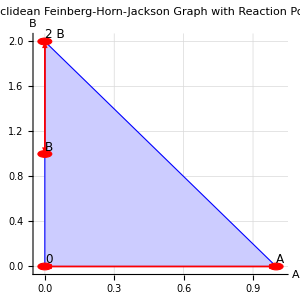

<|Species→{A,B},Reactions→{0→A,A→0,B→2 B,2 B→B},Endotactic→False,StronglyEndotactic→False,StoichiometricSubspace→{{1,0},{-1,0},{0,-1}}|>

```mathematica
(*Example 8.5:Network showing limitations*)
(*Expected:endotactic but NOT strongly endotactic*)
exa5={"0"->"A","A"->"0","B"->"2B","2B"->"B"};
endo[exa5]
```

```mathematica
(*Example 8.6:Weakly reversible network*)
(*Expected:endotactic but NOT strongly endotactic*)
exa6={"A"->"B","B"->"C","C"->"A","2A"->"3B","3B"->"2A"};
endo[exa6]
```

<|Species→{A,B,C},Reactions→{A→B,B→C,C→A,2 A→3 B,3 B→2 A},Endotactic→True,StronglyEndotactic→True,StoichiometricSubspace→{{-1,1,0},{0,-1,1},{1,0,-1},{-2,3,0},{2,-3,0}}|>

```mathematica
(*Additional simple examples for testing*)
simple1={"A"->"B","B"->"A"};
simple2={"A"->"B","B"->"C","C"->"A"};
simple3={"0"->"A","0"->"B"};
simple4={"A"->"2A","2A"->"A"};
simple5={"A"->"2B","2B"->"C","C"->"A"};
```